```mathematica
ClearAll[LineCapped]
LineCapped[line:(Line[{start_, stop_}]), width_]:=
Module[{vec=stop-start, cross={{0, 1}, {-1, 0}}},
Module[{capVec=(cross.vec)/Norm[vec]*width/2},
Module[{return=Sequence[line, Line[{stop-capVec, stop+capVec}]]},
return]]]
```

```mathematica
AngleLine[θ_, length_]:=Line[{{0, 0}, length*{Sin[θ], Cos[θ]}}]
```

```mathematica
AngleArrow[θ_, length_]:=Arrow[{{0, 0}, length*{Sin[θ], Cos[θ]}}]
```

```mathematica
ClearAll[ThreeJet]
ThreeJet[x1in_, x2in_, x3in_]:=
Module[{normalize=2/(x1in+x2in+x3in)},
Module[{x1=normalize*x1in, x2=normalize*x2in, x3=normalize*x3in},
Module[{θ2=ArcCos[(x3^2-x1^2-x2^2)/(2x1*x2)], 
θ3=-ArcCos[(x2^2-x1^2-x3^2)/(2x1*x3)]},
MapThread[LineCapped[AngleLine[#1, #2], .1]&, {{0 ,θ2, θ3}, {x1, x2, x3}}]]]]
```

```mathematica
ThreeJet[x1in_, x2in_, x3in_]:=
Module[{normalize=2/(x1in+x2in+x3in)},
Module[{x1=normalize*x1in, x2=normalize*x2in, x3=normalize*x3in},
Module[{θ2=ArcCos[(x3^2-x1^2-x2^2)/(2x1*x2)], 
θ3=-ArcCos[(x2^2-x1^2-x3^2)/(2x1*x3)]},
MapThread[AngleArrow[#1, #2]&, {{0 ,θ2, θ3}, {x1, x2, x3}}]]]]
```

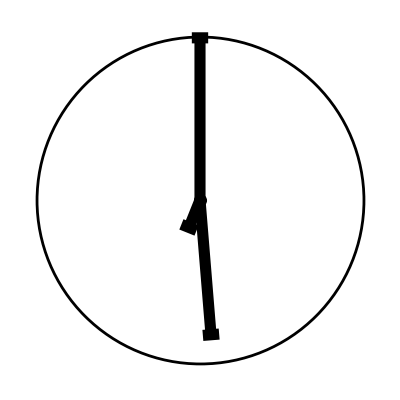

```mathematica
(* 78 *)

me78E1 = 124.01421849901864;
me78E2 = 103.38571762282898;
me78E3 =22.600063877935398;

threeJetA=Graphics[Join[Join[{Black,Thickness[.02], Disk[{0,0}, .04]},ThreeJet[me78E1, me78E2, me78E3], {Thickness[.005],Dashing[{2π/400, 2π/200}], Circle[{0, 0}, 1]}]]]
```

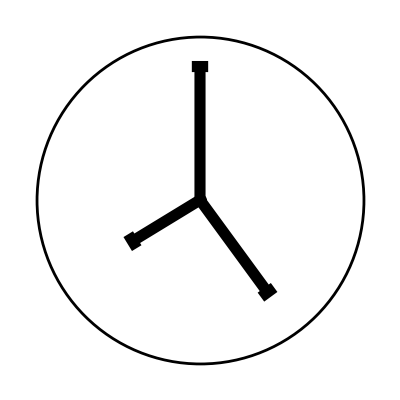

```mathematica
(* 03 *)

me3E1 = 102.06341870844921;
me3E2 =87.460965872998784;
me3E3 =60.475615418549104;

threeJetB=Graphics[Join[Join[{Black,Thickness[.02], Disk[{0,0}, .04]},ThreeJet[me3E1,me3E2, me3E3], {Thickness[.005],Dashing[{2π/400, 2π/200}], Circle[{0, 0}, 1]}]]]
```